Autor: JOE MAMA

# Metody numeryczne (Informatyka)

## Projekt 1

Metoda bisekcji

Napisać procedurę realizującą algorytm metody bisekcji (argumenty:  f, a, b, e).

Korzystając z napisanej procedury:

a) Wyznaczyć wszystkie rzeczywiste pierwiastki wielomianu: f(x)=x^5+4 x^3+2x-8.

b) Wyznaczyć  (z dokładnością 10^-6) najmniejszy dodatni pierwiastek funkcji: h(x)=exp(-x^2) sin x-cos x.

c) Znaleźć (z dokładnością do sześciu cyfr po przecinku) największą liczbę x∈(0,40], dla której jest spełniona nierówność:  10 ln x + 5 ≤  x.

## Rozwiązanie

### Program

```mathematica
bisekcja[f_,a_,b_,e_] := Module[{m,ax,bx},
m = (a+b)/2; ax = a; bx = b;
While[Abs[f[m]]>e, 
If[f[ax]*f[m] < 0, bx=m, ax=m];
m = (ax+bx)/2;
];
Return[m]
]
```

### Przykład testowy

```mathematica
test[x_]:=2x-√(1+x);
bisekcja[test,-1,3,0.001]//N
```

0.640625

### Zadanie a)

```mathematica
f[x_]:=x^5+4 x^3+2x-8
```

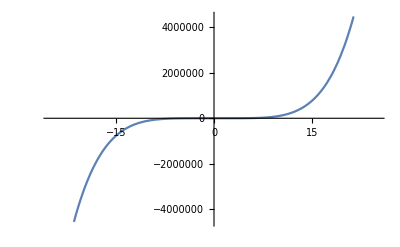

```mathematica
Plot[f[x],{x,-25,25}]
```

```mathematica
(* w przybliżeniu przecięcie OX następuje dla wartości x ∈ <-10, 10> *)
Plot[f'[x],{x,-5000,5000}]
```

-Graphics-

```mathematica
Limit[f'[x],x->-∞]
```

∞

```mathematica
Limit[f'[x],x->∞]
```

∞

```mathematica
(* funkcja jest monotoniczna *)
bisekcja[f,-10,10,10^-6]//N
```

1.04968

### Zadanie b)

```mathematica
h[x_]:=Exp[-x^2]*Sin[x]-Cos[x]
```

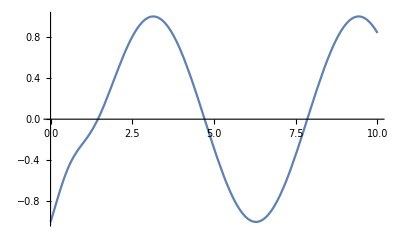

```mathematica
Plot[h[x],{x,0,10}]
```

```mathematica
(* najmniejszy pierwiastek x ∈ <1, 2> *)
bisekcja[h,1,2,10^-6]//N
```

1.44884

### Zadanie c)

```mathematica
(* 10ln(x) + 5 ≤ x  ->  10ln(x) + 5 - x ≤ 0 *)
```

```mathematica
g[x_]:=10Log[x]+5-x
```

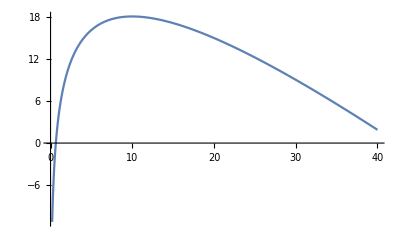

```mathematica
Plot[g[x],{x,0,40}]
```

```mathematica
(* poszukiwana liczba x ∈ <0, 2> *)
bisekcja[g,0,2,10^-6]//N
```

0.647075